```mathematica
L[i_Integer,v_]:=Integrate
```

```mathematica
s[x_,y_]:={a,b}+c{y,-x}
```

SetDelayed::write: Tag List in {y/2,-x/2}[x_,y_] is Protected.

$Failed

```mathematica
τ=Normalize@{Subscript[x, 2]-Subscript[x, 1],Subscript[y, 2]-Subscript[y, 1]}
```

{(-x_1+x_2)/(√(Abs[-x_1+x_2]^2+Abs[-y_1+y_2]^2)),(-y_1+y_2)/(√(Abs[-x_1+x_2]^2+Abs[-y_1+y_2]^2))}

```mathematica
FullSimplify@∫_0^1 s[Subscript[x, 1]+(Subscript[x, 2]-Subscript[x, 1])t,Subscript[y, 1]+(Subscript[y, 2]-Subscript[y, 1])t].τ Sqrt[(Subscript[x, 2]-Subscript[x, 1])^2+(Subscript[y, 2]-Subscript[y, 1])^2]ⅆt
```

∫_0^1 {y/2,-x/2}[x_1-t x_1+t x_2,y_1-t y_1+t y_2].{(-x_1+x_2)/(√(Abs[x_1-x_2]^2+Abs[y_1-y_2]^2)),(-y_1+y_2)/(√(Abs[x_1-x_2]^2+Abs[y_1-y_2]^2))} √((x_1-x_2)^2+(y_1-y_2)^2)ⅆt

```mathematica
A=Table[{Subscript[a, i],Subscript[b, i],Subscript[c, i]},{i,3}]
```

{{a_1,b_1,c_1},{a_2,b_2,c_2},{a_3,b_3,c_3}}

```mathematica
B=Transpose@{
{Subscript[x, 2]-Subscript[x, 3],Subscript[y, 2]-Subscript[y, 3],Subscript[x, 2] Subscript[y, 3]-Subscript[x, 3] Subscript[y, 2]},
{Subscript[x, 3]-Subscript[x, 1],Subscript[y, 3]-Subscript[y, 1],Subscript[x, 3] Subscript[y, 1]-Subscript[x, 1] Subscript[y, 3]},
{Subscript[x, 1]-Subscript[x, 2],Subscript[y, 1]-Subscript[y, 2],Subscript[x, 1] Subscript[y, 2]-Subscript[x, 2] Subscript[y, 1]}
}
```

{{x_2-x_3,-x_1+x_3,x_1-x_2},{y_2-y_3,-y_1+y_3,y_1-y_2},{-x_3 y_2+x_2 y_3,x_3 y_1-x_1 y_3,-x_2 y_1+x_1 y_2}}

```mathematica
A=Inverse@B;
```

```mathematica
Subscript[s, 1][u_,v_]:={A[[1,1]],A[[1,2]]}+A[[1,3]]{u,-v}
```

```mathematica
T=Triangle[{{Subscript[x, 1],Subscript[y, 1]},{Subscript[x, 2],Subscript[y, 2]},{Subscript[x, 3],Subscript[y, 3]}}];
```

```mathematica
Subscript[s, 1][u,v]/.{Subscript[x, 1]->1,Subscript[y, 1]->1,Subscript[x, 2]->2,Subscript[y, 2]->1,Subscript[x, 3]->1,Subscript[y, 3]->2}
```

{-1+u,1-v}

```mathematica
T=T/.{Subscript[x, 1]->1,Subscript[y, 1]->1,Subscript[x, 2]->2,Subscript[y, 2]->1,Subscript[x, 3]->1,Subscript[y, 3]->2};
```

```mathematica
Plot3D[{-1+u,1-v},{u,v}∈T]
```

-Graphics3D-

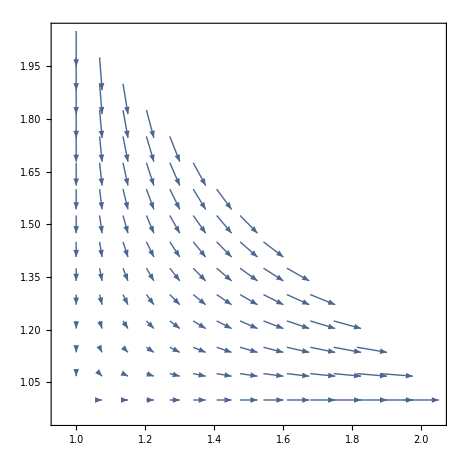

```mathematica
VectorPlot[{-1+u,1-v},{u,v}∈T]
```